```mathematica
Datos
```

```mathematica
Ni=50;
β=10^6;       
Ci=12.08;
Di=0.11;
ηLos=10^(1.6/10);
ηNLos=10^(23/10);
VC=3 10^8;
fc=2.5 10^9;
No=2.0019 10^-12;
Ki=1;
B=50 10^6;
Lxti=0;
Lxts=500;
Lyti=0;
Lyts=500;
Lzti=0;
Lzts=1;
Lxs={500,1000};
Lys={500,500};
Lxi={0,500};
Lyi={0,0};
Lzi={0,0};
Lzs={1,150};
α =2;
λ = 0.01;
h =10;
```

## Li and Joint

```mathematica
jointPDF3D[Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,x_,y_,z_,λ_]:=PDF[ProductDistribution[TruncatedDistribution[{Lxti,Lxts},ExponentialDistribution[λ]],TruncatedDistribution[{Lyti,Lyts},ExponentialDistribution[λ]],TruncatedDistribution[{Lzti,Lzts},ExponentialDistribution[λ]]],{x,y,z}]
di[x_,xi_,y_,yi_,z_,hi_]:=Sqrt[(xi-x)^2+(yi-y)^2+(hi-z)^2];
βeta[x_,xi_,y_,yi_,z_,hi_]:=180/π ArcSin[(hi*Sqrt[(xi-x)^2+(yi-y)^2])/(di[x,xi,y,yi,z,hi] Sqrt[(xi-x)^2+(yi-y)^2+z^2])] ;
Plos[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_]:=1/(1+Ci ⅇ^(-Di ( βeta[x,xi,y,yi,z,hi]-Ci))) ;

Li1[x_,xi_,y_,yi_,hi_,z_,Ci_,Di_,ηLos_,ηNLos_,fc_,VC_]:=Plos[x,xi,y,yi,hi,z,Ci,Di] *((4 Pi fc)/VC)^2 *di[x,xi,y,yi,z,hi]^α *ηLos +( ηNLos *(1- Plos[x,xi,y,yi,hi,z,Ci,Di])*di[x,xi,y,yi,z,hi]^α *((4 Pi fc)/VC)^2) ;

Mi[Ni_,Lxs_,Lys_,Lxi_,Lyi_,Lzs_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,λ_]:= Ni* Abs[NIntegrate[jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,λ],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}]];
```

## Función Objetivo

```mathematica
ptG3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,x_,y_,z_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=(2^((β Mi[Ni,Lxs,Lys,Lxi,Lyi,Lzs,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,λ])/B)-1)*No* Li1[x,xi,y,yi,z,hi,Ci,Di,ηLos,ηNLos,fc,VC]*jointPDF3D[Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,x,y,z,λ];

ptGNint3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=NIntegrate[ptG3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B, Ni,x,y,z,xi,yi,hi,No,ηLos,ηNLos,fc,VC,λ],{x,Lxi,Lxs},{y,Lyi,Lys},{z,Lzi,Lzs}];
ptTotalKiUAVs3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=Sum[ptGNint3D[Ci,Di,Lxs[[i]],Lys[[i]],Lzs[[i]],Lxi[[i]],Lyi[[i]],Lzi[[i]],Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi[[All,i]],yi[[All,i]],hi,No,ηLos,ηNLos,fc,VC,λ],{i,1,Ki}];
```

## Llama la función

```mathematica
Objetivo1[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_ ,Ni_,xi_,yi_,hi_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=Module[{},
xMod= ptTotalKiUAVs3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xi,yi,hi,No,ηLos,ηNLos,fc,VC,λ];
Return[xMod];
]
```

## PSO-E-3D

```mathematica
PSOE3D[Ci_,Di_,Lxs_,Lys_,Lzs_,Lxi_,Lyi_,Lzi_,Lxts_,Lyts_,Lzts_,Lxti_,Lyti_,Lzti_,β_,B_,h_,Ni_,No_,ηLos_,ηNLos_,fc_,VC_,λ_]:=Module[{},
iteration = 3;
popSize= 2000;
(*Parametrizaion of PSO*)
tao=1;
tao1=0.2;
inercia1=0.5;
memorial1=2;
cooperacion1=3;
perturbacion1=0.1;
(*Límites de las variables*)
Dmin={200,200,10};
Dmax={300,300,200};
(*Dmin=ConstantArray[0,3*Ki];
Dmax=ConstantArray[200,3*Ki];*)
(*Dmin= {0,0,0} ;
Dmax ={200,200,200} ;*)
D1=Length [Dmin];
xx=ConstantArray[0, {popSize,D1}];
v=ConstantArray[0, {popSize, D1}]; 
fitness=ConstantArray[0,popSize];
(*Posicion inicial de las particulas*)
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=(Dmax[[jj]]-Dmin[[jj]])RandomReal[{0,1}, popSize]+Dmin[[jj]]
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC,λ];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=xx[[indgbest]];
fpbest=fitness;
xpbest=xx;
OF=ConstantArray[0, iteration];
For[count1=1, count1≤iteration, count1++,
OF[[count1]]=fgbest;
inercia = inercia1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
inercia=Clip[inercia,{0,1}];
memoria=memorial1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
memoria=Clip[memoria,{0,1}];
cooperacion=cooperacion1+tao*RandomReal[NormalDistribution[0,1],{popSize,D1}];
cooperacion=Clip[cooperacion,{0,1}];
xgbest=ConstantArray[xgbest,Length[xx]];
v=inercia*v+memoria*(xpbest-xx)+cooperacion*(xgbest-xx);
xx=xx+v;
xgbest=xgbest[[1]];
For[jj=1, jj<=D1, jj++,
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y<Dmin[[jj]]]->Dmin[[jj]]];
xx[[All,jj]]=ReplacePart[xx[[All,jj]],Position[xx[[All,jj]],y_/;y>Dmax[[jj]]]->Dmax[[jj]]];
];
fitness=Objetivo1[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,Ni,xx[[All,1;;Ki]],xx[[All,Ki+1;;2*Ki]],h,No,ηLos,ηNLos,fc,VC,λ];
positions=Flatten[Position[Thread[fitness<fpbest],True]];
xpbest[[positions]]=xx[[positions]];
    fpbest[[positions]]=fitness[[positions]];
{fgbest,indgbest}=Take[Flatten[MinimalBy[Transpose[{fitness,Range[popSize]}],First]],2];
xgbest=Flatten[xx[[indgbest]]];
perturbacion=perturbacion1+tao1*Flatten[RandomReal[NormalDistribution[0,1],{1,Length[xgbest]}]];
perturbacion=Clip[perturbacion,{0,1}];
aux=xgbest+perturbacion;
aux={aux};
c1=Objetivo1[aux];
c2=c1[[1]];
If[fgbest>c2,
xgbest=aux;
xgbest=xgbest[[1]];
fgbest=Objetivo1[aux];
fgbest=fgbest[[1]];
];
];
Return[fgbest];
]
```

```mathematica
PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,h,Ni,No,ηLos,ηNLos,fc,VC,λ]
```

```mathematica
AbsoluteTiming[Fig3D1=ParallelTable[{h,PSOE3D[Ci,Di,Lxs,Lys,Lzs,Lxi,Lyi,Lzi,Lxts,Lyts,Lzts,Lxti,Lyti,Lzti,β,B,h,Ni,No,ηLos,ηNLos,fc,VC,λ]},{h,5,200,5}]]
```

```mathematica
AbsoluteTiming[results=Table[{LztsValue,ParallelTable[{h,PSOE3D[Ci,Di,Lxs,Lys,LztsValue,Lxi,Lyi,Lzi,Lxts,Lyts,LztsValue,Lxti,Lyti,Lzti,β,B,h,Ni,No,ηLos,ηNLos,fc,VC,λ]},{h,5,200,5}]},{LztsValue,{1,50,100,150}}]]
```

Part::partd: Part specification 1⟦1⟧ is longer than depth of object.

$Aborted

```mathematica
Export["C:\\Users\\adm-wolfram\\Documents\\Resultados\\Paper-Revista\\Expon-EPSO-H-150.mat",Fig3D1];
```

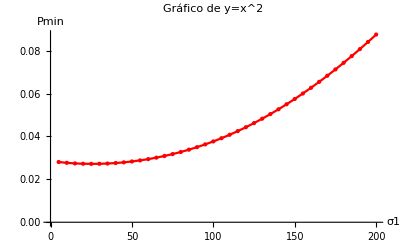

```mathematica
ListPlot[Fig3D1,Joined->True,Mesh->All,PlotStyle->Directive[Red,PointSize[Medium]],AxesLabel->{"σ1","Pmin"},PlotLabel->"Gráfico de y=x^2"]
```